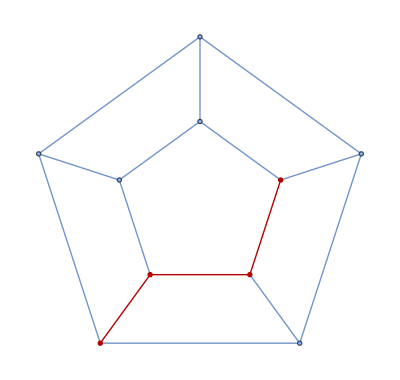
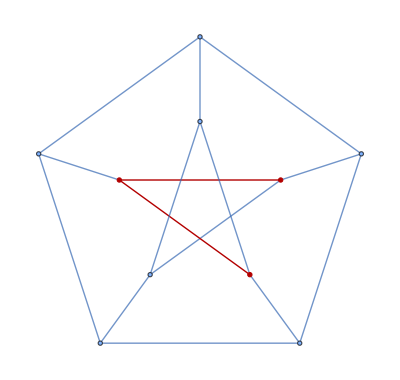
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
FindRadiusPath[g_?UndirectedGraphQ]:=Module[{c=First@GraphCenter[g],d,v,pos},d=Table[GraphDistance[g,c,u],{u,VertexList[g]}];
pos=First@Position[d,Max[d]];
v=First@Part[VertexList[g],pos];
PathGraph[FindShortestPath[g,c,v]]]
Table[HighlightGraph[#,FindRadiusPath[#]]&[PetersenGraph[5,i,VertexSize->Tiny]],{i,3}]
```

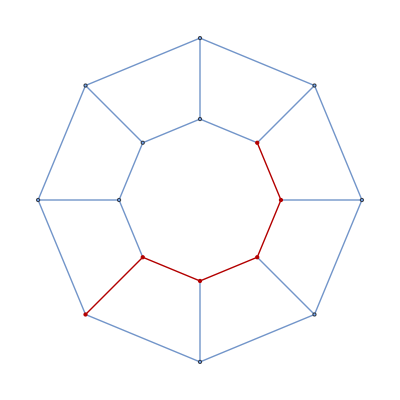
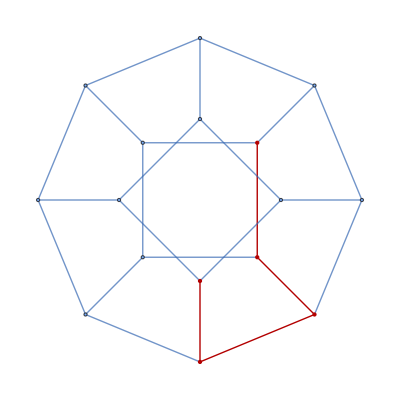
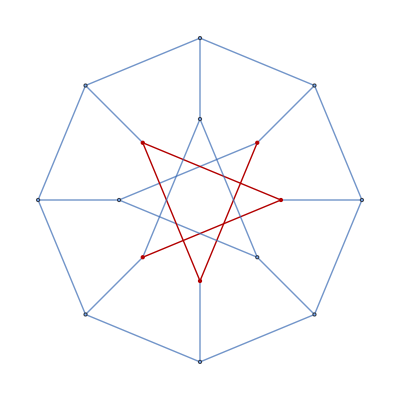
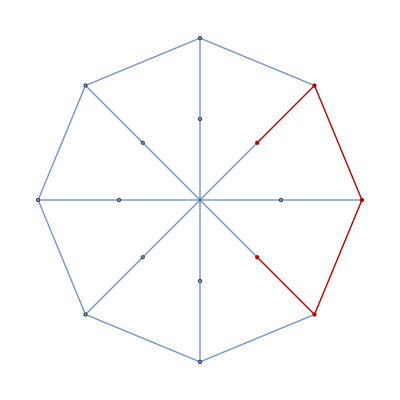

```mathematica
FindDiameterPath[g_?UndirectedGraphQ]:=Module[{d=GraphDistanceMatrix[g],u,v,pos},pos=First@Position[d,Max[d]];
{u,v}=Part[VertexList[g],pos];
PathGraph[FindShortestPath[g,u,v]]]
Table[HighlightGraph[#,FindDiameterPath[#]]&[PetersenGraph[8,i,VertexSize->Tiny]],{i,4}]
```

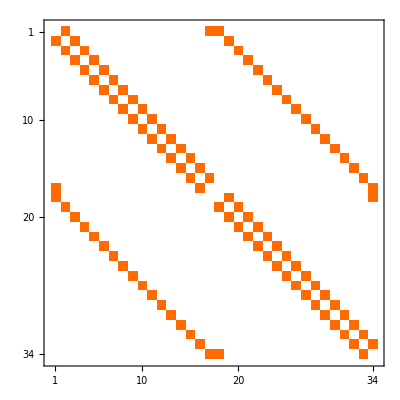
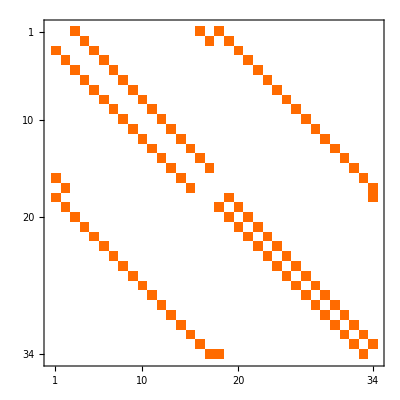
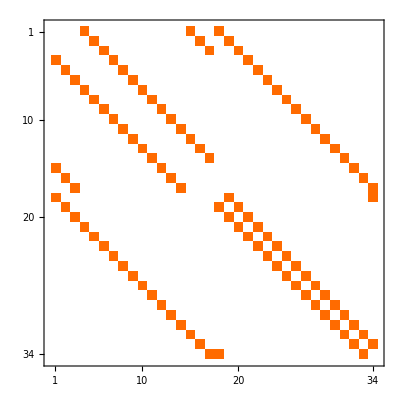
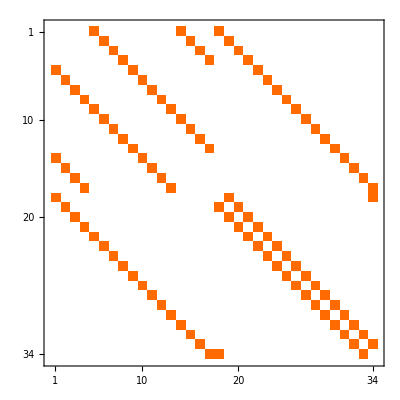
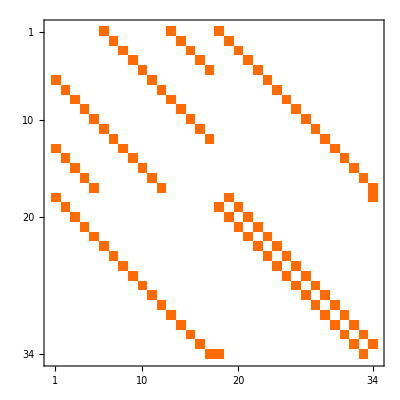
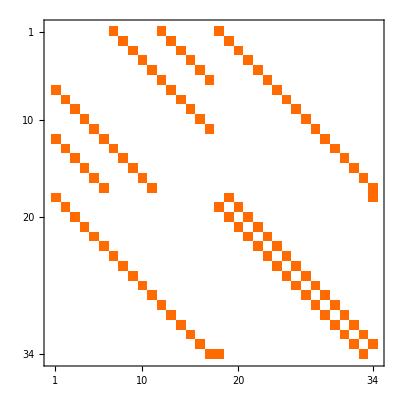
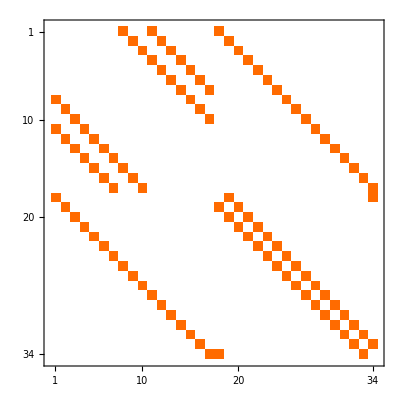
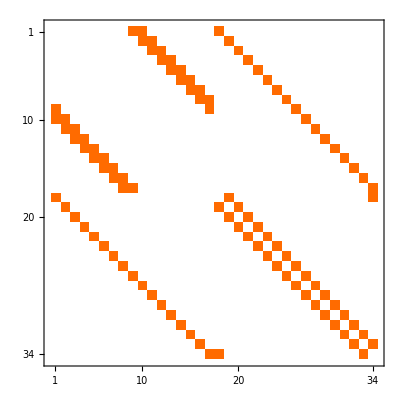
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[MatrixPlot[AdjacencyMatrix[PetersenGraph[17,i]]],{i,10}]
```